## Function Definitions

```mathematica
lowLim=1*^3; (* eV *)
uplim=1*^12; (* eV *)

a0=5.291772101121111395947216558438464*^-11; (* m *)
R=13.605693122994; (* eV *)
α=7.2973525755230202568508027295271584628*^-3;
eRestMass=0.51099895*^6; (* eV *)
lightspeed=2.99792458*^8; (* m/s *)
a=0.3;
b=0.7;
```

```mathematica
t[T_,B_]:=T/B;
S[B_,nocc_]:=4π a0^2 nocc(R/B)^2;
(* The ξ values from Clementi papers already take into account ratio of Zeff and n *)
Cf[ξ1_,ξ2_]:=a ξ1^2/2+b ξ2^2/2;
c[B_,ξ1_,ξ2_]:=(Cf[ξ1,ξ2]/B)2 R;
```

```mathematica
σ[T_,B_,ξ1_,ξ2_,nocc_]:=Piecewise[{{0.,T/B<1},{S[B,nocc]/(t[T,B]+c[B,ξ1,ξ2])(1/2(1-1/t[T,B]^2)Log[t[T,B]]+(1-1/t[T,B])-Log[t[T,B]]/(t[T,B]+1)),T/B≥1}}];
```

```mathematica
tprime[T_]:=T/eRestMass;
bprime[B_]:=B/eRestMass;
betaT2[T_]:=1-1/(1+tprime[T])^2;
betaB2[B_]:=1-1/(1+bprime[B])^2;
```

```mathematica
sigmak0[T_,B_,ξ1_,ξ2_,nocc_]:=(4π a0^2 α^4 nocc)/((betaT2[T]+c[B,ξ1,ξ2]betaB2[B])2bprime[B]);
lastsigmak0[T_,B_,ξ1_,nocc_]:=(4π a0^2 α^4 nocc)/((betaT2[T]+(ξ1^2/2(2 R)/B) betaB2[B])2bprime[B]);
A1[T_,B_]:=1/(t[T,B]+1)(1+2tprime[T])/(1+tprime[T]/2)^2;
A2[T_,B_]:=(t[T,B]-1)/2 bprime[B]^2/(1+tprime[T]/2)^2;
A3[T_,B_]:=Log[betaT2[T]/(1-betaT2[T])]-betaT2[T]-Log[2bprime[B]];
```

```mathematica
(*σrel[T_,B_,ξ1_,ξ2_,nocc_]:=Piecewise[{{0.,T/B<1},{(4π a0^2 α^4 nocc)/((betaT2[T]+c[B,ξ1,ξ2]betaB2[B])2bprime[B])(1/2(Log[betaT2[T]/(1-betaT2[T])]-betaT2[T]-Log[2bprime[B]])(1-1/t[T,B]^2)+1-1/t[T,B]-Log[t[T,B]]/(t[T,B]+1)(1+2tprime[T])/(1+tprime[T]/2)^2+bprime[B]^2/(1+tprime[T]/2)^2(t[T,B]-1)/2),T/B≥1}}];*)
σrel[T_,B_]:=Piecewise[{{0.,T/B<1},{(A3[T,B]/2(1-1/t[T,B]^2)+1-1/t[T,B]+A2[T,B]-A1[T,B]Log[t[T,B]]),T/B≥1}}];
```

## Test Calculation Against Paper

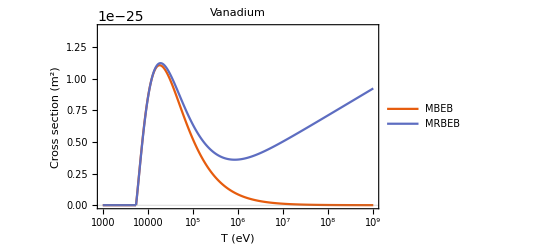

```mathematica
ξ1=22.4256;
ξ2=8.0907;

Bind=5463.76; (* eV *)
Z=23;
nocc=2;
LogLinearPlot[{σ[en,Bind,ξ1,ξ2,nocc],σrel[en,Bind,ξ1,ξ2,nocc]},{en,lowLim,uplim},PlotRange->{0.,1400*^-28},PlotPoints->500, PlotTheme->"Scientific",PlotLegends->{"MBEB","MRBEB"},PlotLabel->"Vanadium",FrameLabel->{"T (eV)","Cross section (m^2)"},LabelStyle->{18}]
```

## Calculate Total Cross Sections

```mathematica
(*18 Ar: 3.2060, 0.3263, 0.2507, 0.2486, 0.0292, 0.0159, 0.0158*)
(*8 O: 0.5320, 0.0285, 0.0071, 0.0071*)
(*7 N: 0.4016, 0.0244, 0.0092, 0.0092*)
```

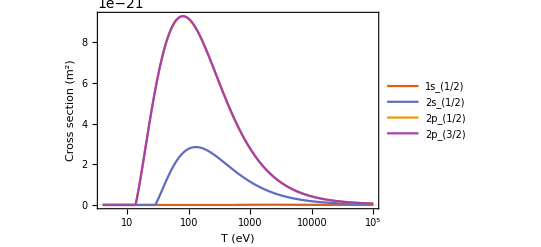

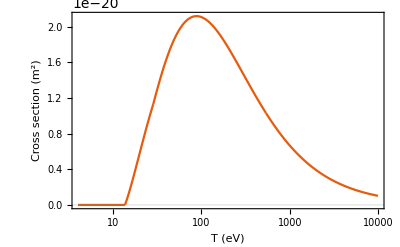

1.83582×10^-21

```mathematica
(*O*)
(*1s1/2 -> 2s1/2*)
ξ1=7.6579;
ξ2=2.2458;
Bind=538.; (* eV *)
nocc=2;
o1s=σrel[en,Bind,ξ1,ξ2,nocc];

(*2s1/2 -> 2p1/2*)
ξ1=2.2458;
ξ2=2.2266;
Bind=28.48; (* eV *)
nocc=2;
o2s=σrel[en,Bind,ξ1,ξ2,nocc];

(*2p1/2 -> 2p3/2*)
ξ1=2.2266;
ξ2=2.2266;
Bind=13.63; (* eV *)
nocc=2;
o2p12=σrel[en,Bind,ξ1,ξ2,nocc];

(*2p3/2*)
ξ1=2.2266;
Bind=13.62; (* eV *)
nocc=2;
o2p32=Piecewise[{{0.,en/Bind<1},{(4π a0^2 α^4 nocc)/((betaT2[en]+(ξ1^2/2(2 R)/Bind) betaB2[Bind])2bprime[Bind])(1/2(Log[betaT2[en]/(1-betaT2[en])]-betaT2[en]-Log[2bprime[Bind]])(1-1/t[en,Bind]^2)+1-1/t[en,Bind]-Log[t[en,Bind]]/(t[en,Bind]+1)(1+2tprime[en])/(1+tprime[en]/2)^2+bprime[Bind]^2/(1+tprime[en]/2)^2(t[en,Bind]-1)/2),en/Bind≥1}}];
oinout = o1s+o2s+o2p12+o2p32;
LogLinearPlot[{o1s,o2s,o2p12,o2p32},{en,4,100000},PlotRange->All,PlotPoints->500,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
LogLinearPlot[oinout,{en,4,10000},PlotRange->All,PlotPoints->500,PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
oinout/.en->5000.
```

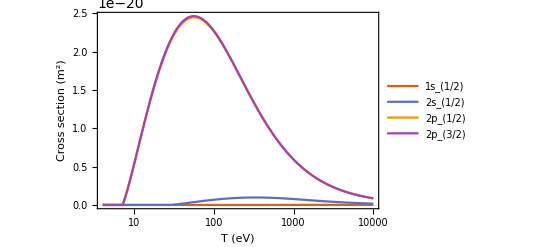

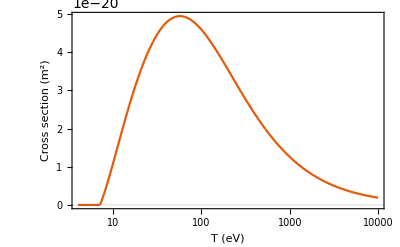

```mathematica
(*O*)
(*2p3/2 -> 2p1/2*)
ξ1=2.2266;
ξ2=2.2266;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p32=σrel[en,Bind,ξ1,ξ2,nocc];

(*2p1/2 -> 2s1/2*)
ξ1=2.2266;
ξ2=2.2458;
Bind=0.0071*1000.; (* eV *)
nocc=2;
o2p12=σrel[en,Bind,ξ1,ξ2,nocc];

(*2s1/2 -> 1s1/2*)
ξ1=2.2458;
ξ2=7.6579;
Bind=0.0285*1000.; (* eV *)
nocc=2;
o2s=σrel[en,Bind,ξ1,ξ2,nocc];

(*1s1/2*)
ξ1=7.6579;
Bind=0.5320*1000.; (* eV *)
nocc=2;
o1s=Piecewise[{{0.,en/Bind<1},{(4π a0^2 α^4 nocc)/((betaT2[en]+(ξ1^2/2(2 R)/Bind) betaB2[Bind])2bprime[Bind])(1/2(Log[betaT2[en]/(1-betaT2[en])]-betaT2[en]-Log[2bprime[Bind]])(1-1/t[en,Bind]^2)+1-1/t[en,Bind]-Log[t[en,Bind]]/(t[en,Bind]+1)(1+2tprime[en])/(1+tprime[en]/2)^2+bprime[Bind]^2/(1+tprime[en]/2)^2(t[en,Bind]-1)/2),en/Bind≥1}}];
ooutin = o1s+o2s+o2p12+o2p32;
LogLinearPlot[{o1s,o2s,o2p12,o2p32},{en,4,10000},PlotRange->All,PlotPoints->500,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross section (m^2)"}]
LogLinearPlot[ooutin,{en,4,10000},PlotRange->All,PlotTheme->"Scientific",PlotPoints->500,FrameLabel->{"T (eV)","Cross section (m^2)"}]
```

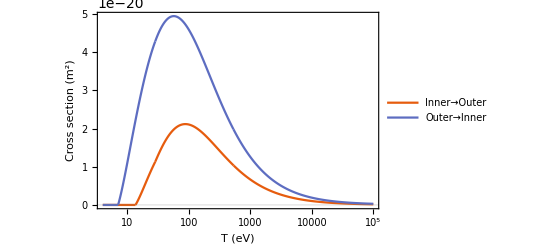

```mathematica
LogLinearPlot[{oinout,ooutin},{en,4,100000},PlotRange->All,PlotTheme->"Scientific",PlotPoints->500,FrameLabel->{"T (eV)","Cross section (m^2)"},PlotLegends->{"Inner→Outer","Outer→Inner"}]
```

## Collisional Ionization Rate

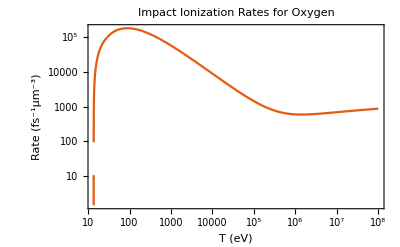

```mathematica
v=299788583.58;
nair=0.27*^26;
nbeam=0.10817025341*^25; (*For 10 pC, 10fs bunch, 100 MeV*)
LogLogPlot[v*nair*nbeam*oinout*(1*^-15)*(1*^-18),{en,4,100*^6},PlotRange->All,PlotTheme->"Scientific",PlotPoints->500,FrameLabel->{"T (eV)","Rate (fs^-1μm^-3)"},LabelStyle->{18},PlotLabel->"Impact Ionization Rates for Oxygen"]
```

## Cross Section for Argon

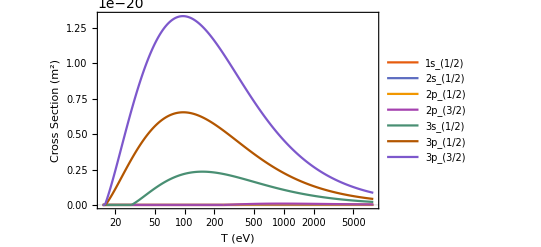

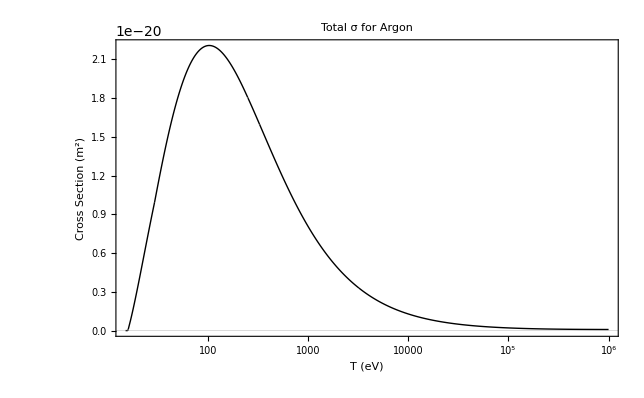

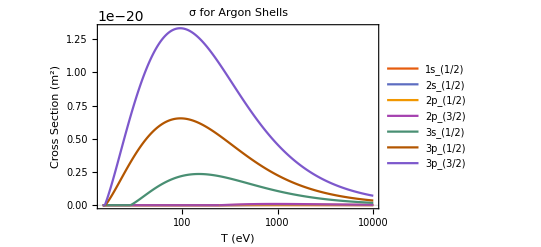

```mathematica
(*Ar*)
(*1s1/2 -> 2s1/2*)
ξ1=17.417/1.;
ξ2=14.572/2.;
Bind=3206.3; (* eV *)
nocc=2;
o1s=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*2s1/2 -> 2p1/2*)
ξ1=14.572/2.;
ξ2=13.34/2.;
Bind=326.5; (* eV *)
nocc=2;
o2s=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*2p1/2 -> 2p3/2*)
ξ1=13.34/2.;
ξ2=13.304/2.;
Bind=250.6; (* eV *)
nocc=2;
o2p12=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*2p3/2 -> 3s1/2*)
ξ1=13.304/2.;
ξ2=9.519/3.;
Bind=248.5; (* eV *)
nocc=4;
o2p32=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*3s1/2 -> 3p1/2*)
ξ1=9.519/3.;
ξ2=7.541/3.;
Bind=29.24; (* eV *)
nocc=2;
o3s12=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*3p1/2 -> 3p3/2*)
ξ1=7.541/3.;
ξ2=7.502/3.;
Bind=15.94; (* eV *)
nocc=2;
o3p12=sigmak0[en,Bind,ξ1,ξ2,nocc]σrel[en,Bind];

(*3p3/2*)
ξ1=7.502/3.;
Bind=15.76; (* eV *)
nocc=4;
o3p32=lastsigmak0[en,Bind,ξ1,nocc]σrel[en,Bind];

oinout = o1s+o2s+o2p12+o2p32+o3s12+o3p12+o3p32;
LogLinearPlot[{o1s,o2s,o2p12,o2p32,o3s12,o3p12,o3p32},{en,15,8000},PlotRange->All,PlotPoints->500,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)","3s_(1/2)","3p_(1/2)","3p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross Section (m^2)"}]
total=LogLinearPlot[oinout,{en,15,1*^6},PlotRange->All,PlotPoints->500,PlotStyle->{Thick,Black},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross Section (m^2)"},PlotLabel->"Total σ for Argon",LabelStyle->{Black,18},PlotRange->{0,Automatic},Background->White]

shells=LogLinearPlot[{o1s,o2s,o2p12,o2p32,o3s12,o3p12,o3p32},{en,15,10000},PlotRange->All,PlotPoints->500,PlotStyle->Thick,PlotLegends->{"1s_(1/2)","2s_(1/2)","2p_(1/2)","2p_(3/2)","3s_(1/2)","3p_(1/2)","3p_(3/2)"},PlotTheme->"Scientific",FrameLabel->{"T (eV)","Cross Section (m^2)"},LabelStyle->{Black,18},PlotLabel->"σ for Argon Shells",Background->White,
Epilog->Inset[
LogLinearPlot[{o1s,o2s,o2p12,o2p32},{en,200,8000},PlotRange->All,PlotPoints->500,PlotStyle->Thick,PlotTheme->"Scientific",LabelStyle->{Black,18}],ImageScaled[{0.99,0.92}], {Right,Top},Scaled[{0.5,0.5}]]]
```

InterpolatingFunction[…]

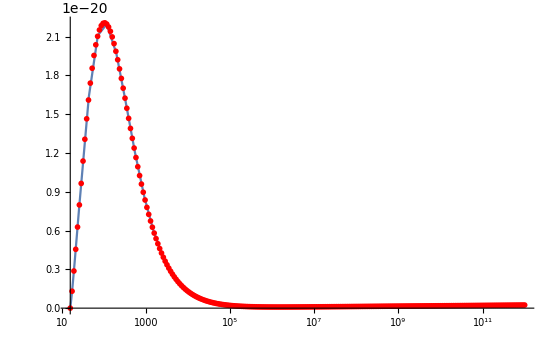

```mathematica
np = 250;
emin=15.76;
emax=1*^12;
slope=(np-1)/Log10[emax/emin];
energies=Table[emin 10^((i-1)/slope),{i,1,np,1}];
sig[en_]:=oinout;
points=Table[{en,sig[en]},{en,energies}];
(*InterpolatingPolynomial[points,en];*)
(*LogLinearPlot[Evaluate[InterpolatingPolynomial[points,en]],{en,emin,emax},PlotRange->2.5*^-20,Epilog->{Red,Map[Point,points]}]*)
Interpolation[points]
Show[LogLinearPlot[%[en],{en,emin,emax},PlotRange->All],ListLogLinearPlot[points,PlotStyle->Red]]
(*ListLogLinearPlot[points,PlotRange->All]*)
(*Plot[Evaluate[InterpolatingPolynomial[points,en]],{en,15.76,1*^12}]*)
```